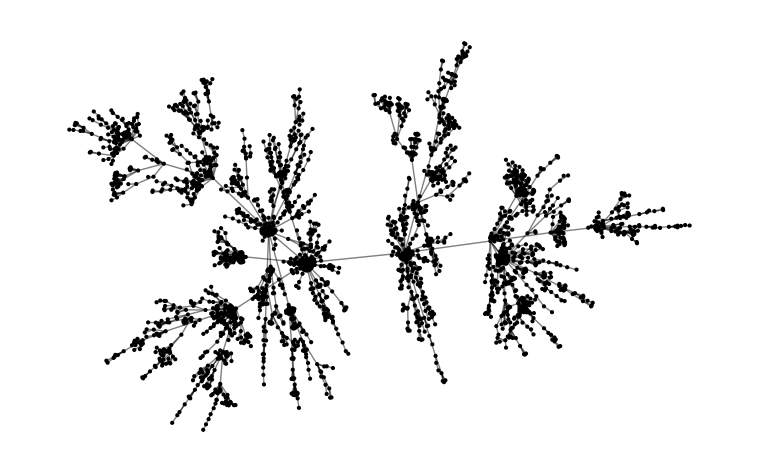

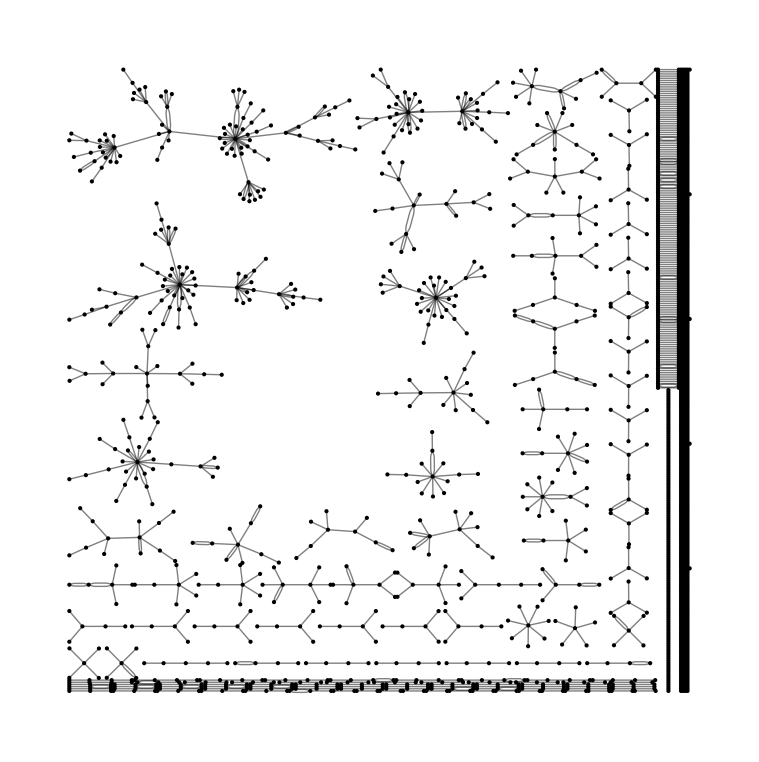

```mathematica
GPlotter[g_] := GraphPlot[g,
EdgeStyle->Arrowheads[Small],  
VertexShapeFunction->Function[{p},{Black,Point[p]}],
EdgeShapeFunction->Function[{p},{Black,Line[p]}],
Method->"SpringElectricalEmbedding"
]
RemoveEdges[g0_,p0_] := Module[{g=g0, p=p0, edgesToRemove},
edgesToRemove=RandomSample[EdgeList[g],Round[p EdgeCount[g]]];
EdgeDelete[g,edgesToRemove]
]
(* Barabasi Albert *)
ba = RandomGraph[BarabasiAlbertGraphDistribution[2500, 1]];
GPlotter[ba]
GPlotter[RemoveEdges[DirectedGraph[ba], .8]]
```

```mathematica
adj = AdjacencyMatrix[ba]
```

SparseArray[…]

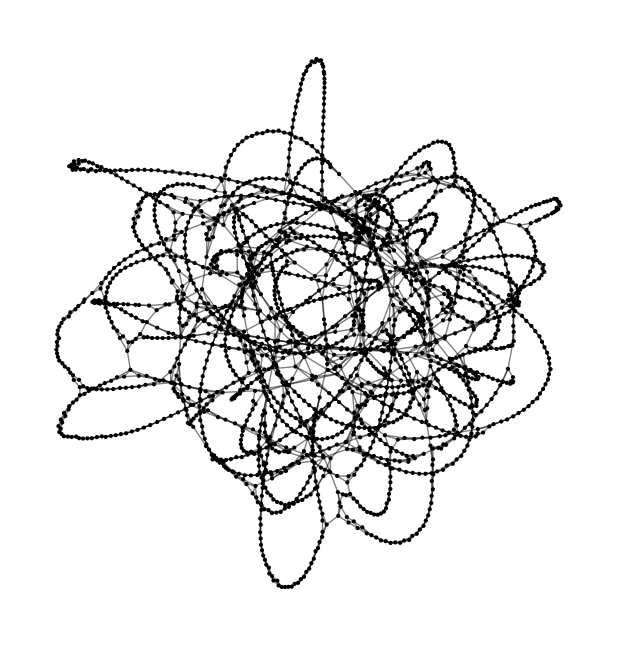

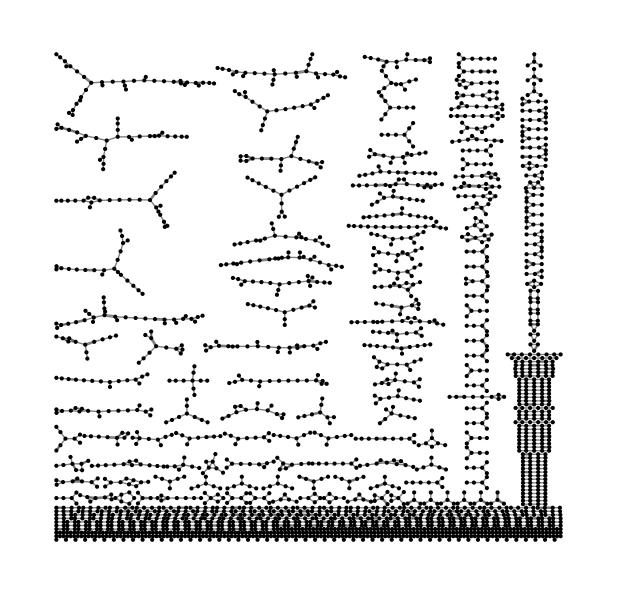

```mathematica
ws = RandomGraph[WattsStrogatzGraphDistribution[2500,0.03]];
GPlotter[ws]
GPlotter[RemoveEdges[DirectedGraph[ws], 0.8]]
```

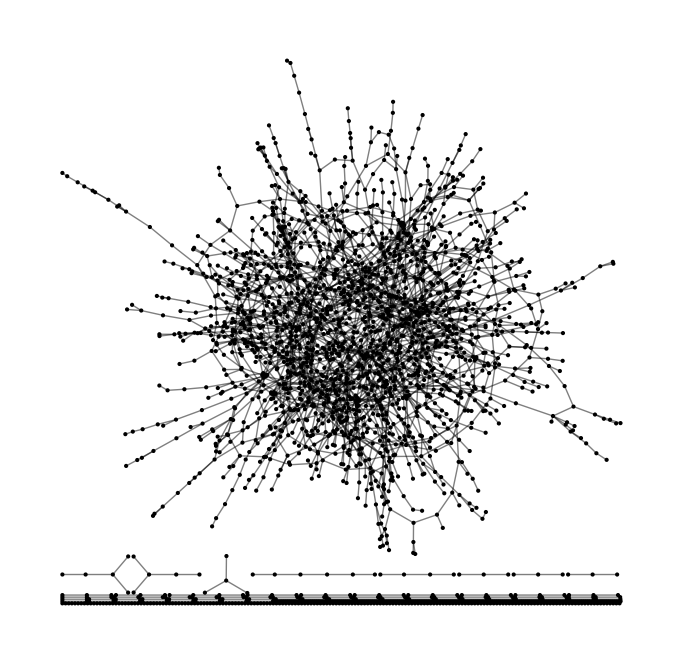

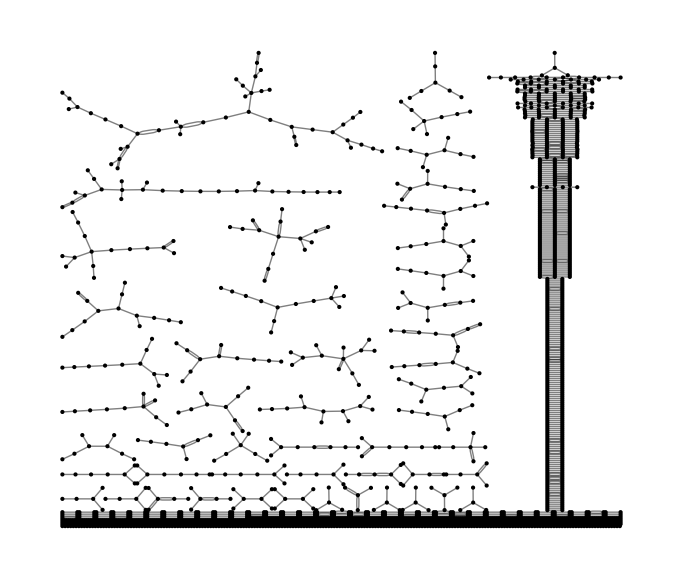

```mathematica
er = RandomGraph[BernoulliGraphDistribution[2500, 2/2500]];
GPlotter[er]
GPlotter[RemoveEdges[DirectedGraph[er], .8]]
```

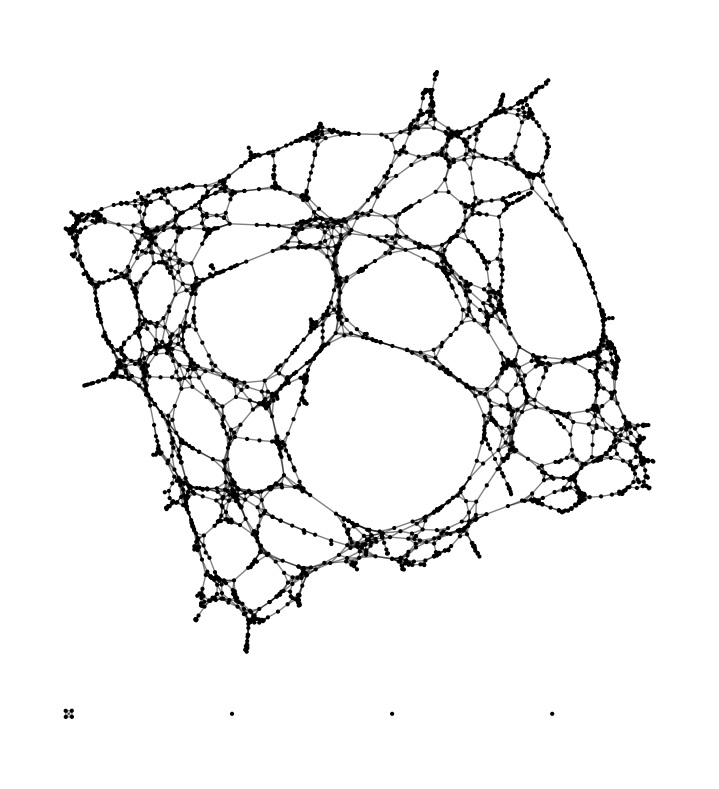

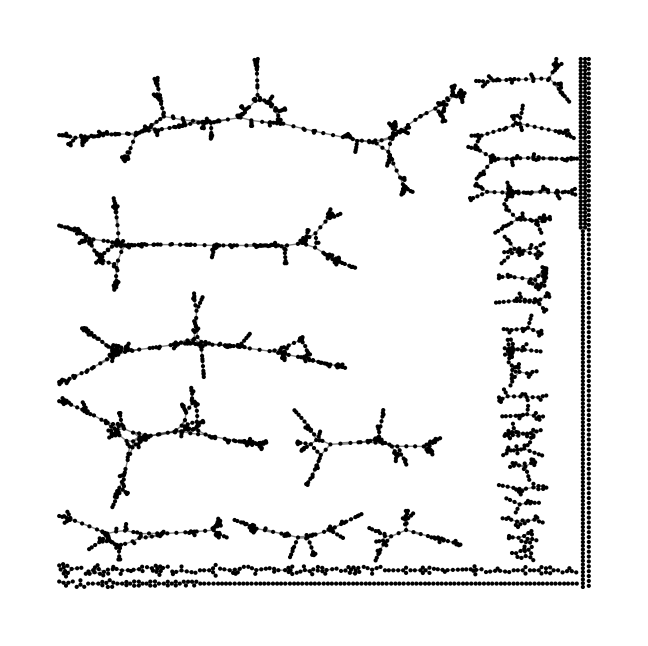

```mathematica
rg = AdjacencyGraph[AdjacencyMatrix[RandomGraph[SpatialGraphDistribution[2500, .03]]]];
GPlotter[rg]
GPlotter[RemoveEdges[DirectedGraph[rg], 0.8]]
```

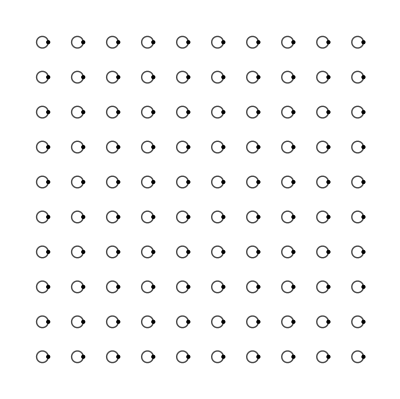

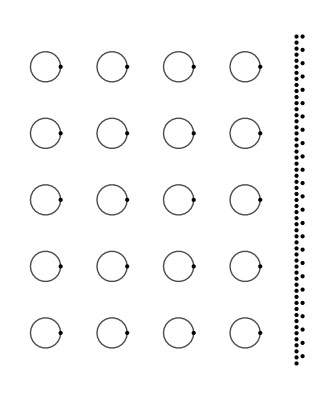

```mathematica
ident = IdentityMatrix[100];
ig = AdjacencyGraph[ident];
GPlotter[ig]
GPlotter[RemoveEdges[ig, .8]]
```